{Binding Energy cs, bs, cc, bc, bb}

-0.024638

-0.0319309

-0.0771545

-0.10134

-0.127854

{Ωcc 1/2+}

{3.72635,4.49139,{3.07333,2.93896,2.45719,2.04279}}

{0.476255}

{{0.326422},{0.309184},{0.863504}}

{Ωcc^* 3/2+}

{3.81988,4.68746,{3.07616,2.94672,2.46928,2.04279}}

{0.495399}

{{0.124097},{0.117544},{0.328282}}

{Ωbb 1/2+}

{10.4079,3.83029,{3.06173,2.90782,2.41366,2.04279}}

{0.450231}

{{0.0277797},{0.0263127},{0.0734873}}

{Ωbb^* 3/2+}

{10.4509,3.9654,{3.06441,2.9149,2.42292,2.04279}}

{0.465408}

{{-0.282537},{-0.267616},{-0.747411}}

{Ωccc 3/2+}

{4.84099,4.2212,{3.06902,2.92725,2.43993,2.04279}}

{0.680664}

{{0.548595},{0.519625},{1.45123}}

{Ωccb 1/2+}

{8.11201,3.74521,{3.05994,2.90313,2.40773,2.04279}}

{0.439787}

{{0.248989},{0.23584},{0.658666}}

{Ωccb^* 3/2+}

{8.13339,3.83212,{3.06176,2.90792,2.41378,2.04279}}

{0.44896}

{{0.326881},{0.309619},{0.864718}}

{Ωcbb 1/2+}

{11.3734,3.18239,{3.0458,2.86706,2.36644,2.04279}}

{0.111755}

{{-0.0999875},{-0.0947073},{-0.264503}}

{Ωcbb^* 3/2+}

{11.4024,3.31322,{3.04951,2.87633,2.37636,2.04279}}

{0.114238}

{{0.109689},{0.103897},{0.290168}}

{Ωbbb 3/2+}

{14.6262,2.58744,{3.02444,2.816,2.31855,2.04279}}

{0.283488}

{{-0.0949393},{-0.0899256},{-0.251149}}

{Mass Spectrum}

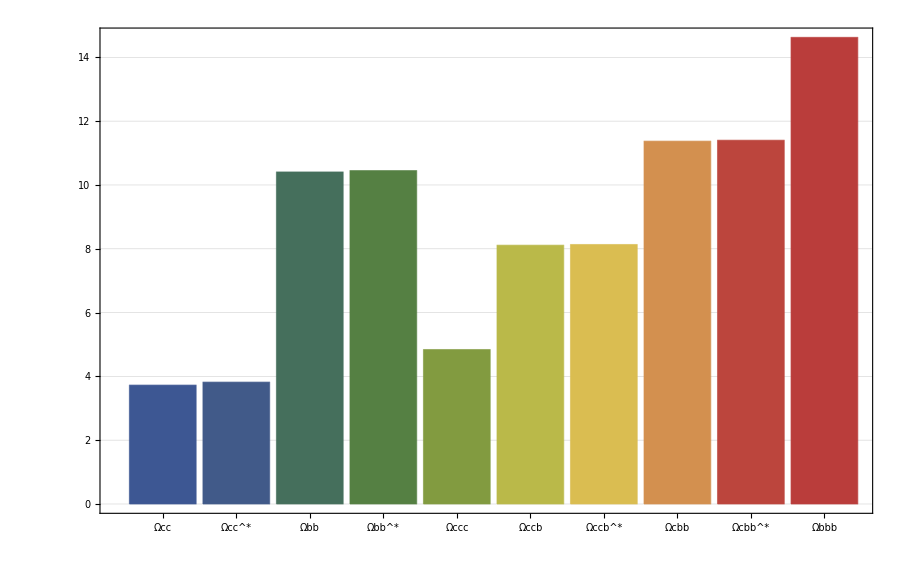

{Charge Radius}

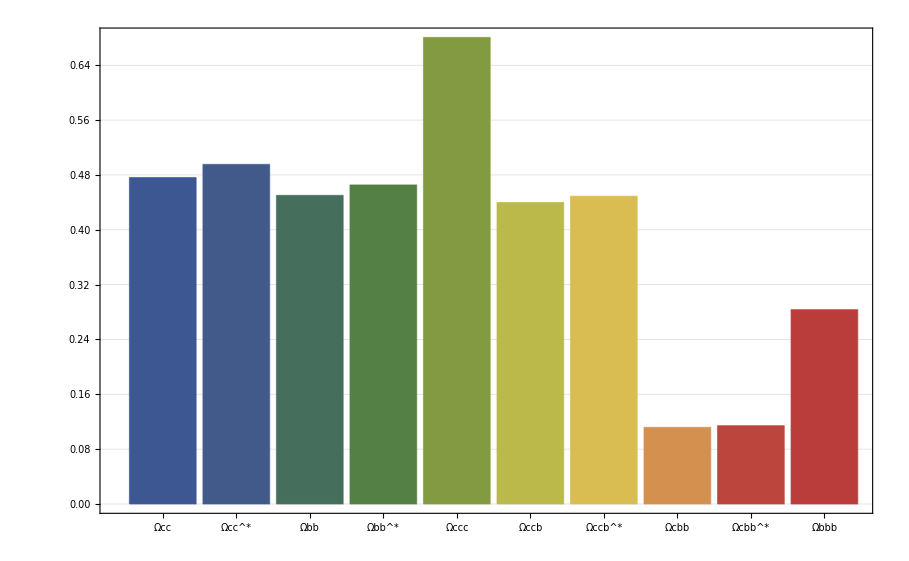

{Magnetic Moment}

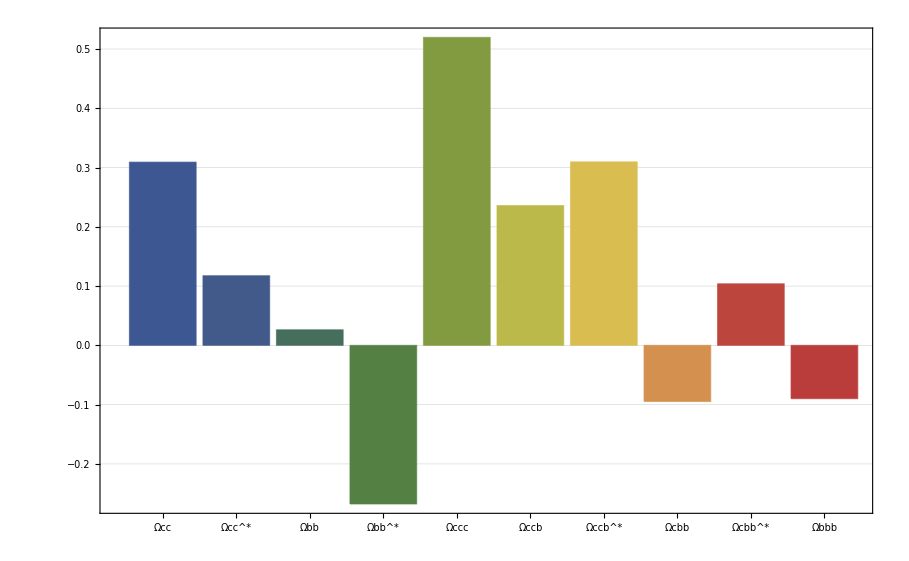

```mathematica
Get[NotebookDirectory[]<>"MITBagModel.wl"]

Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];
γμN=2.7928473446;

{"Binding Energy cs, bs, cc, bc, bb"}
Bcs=-(First[Hadron[{0,1,1,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}},0]]-2.112)/2
Bbs=-(First[Hadron[{1,0,1,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-5.415)/2
Bcc=-(First[Hadron[{0,2,0,0},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}},0]]-3.097)/2
Bbc=-(First[Hadron[{1,1,0,0},{{0,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-6.332)/2
Bbb=-(First[Hadron[{2,0,0,0},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-9.460)/2

{"Ωcc 1/2+"}
Ωcc=Hadron[{0,2,1,0},{{0,0,0,0},{0,-8/3,32/3,0},{0,0,0,0},{0,0,0,0}},2Bcs+Bcc]
rΩcc=ChargeRadius[{0,2,1,0,0},{0,0,0,0,0},Ωcc];
μΩcc=MagneticMoment[{0,4/3,-1/3,0,0},{0,0,0,0,0},Ωcc];
{rΩcc}
{{μΩcc},{μΩcc/μNp},γμN{μΩcc/μNp}}

{"Ωcc^* 3/2+"}
ΩccStar=Hadron[{0,2,1,0},{{0,0,0,0},{0,-8/3,-16/3,0},{0,0,0,0},{0,0,0,0}},2Bcs+Bcc]
rΩccStar=ChargeRadius[{0,2,1,0,0},{0,0,0,0,0},ΩccStar];
μΩccStar=MagneticMoment[{0,2,1,0,0},{0,0,0,0,0},ΩccStar];
{rΩccStar}
{{μΩccStar},{μΩccStar/μNp},γμN{μΩccStar/μNp}}

{"Ωbb 1/2+"}
Ωbb=Hadron[{2,0,1,0},{{-8/3,0,32/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs+Bbb]
rΩbb=ChargeRadius[{2,0,1,0,0},{0,0,0,0,0},Ωbb];
μΩbb=MagneticMoment[{4/3,0,-1/3,0,0},{0,0,0,0,0},Ωbb];
{rΩbb}
{{μΩbb},{μΩbb/μNp},γμN{μΩbb/μNp}}

{"Ωbb^* 3/2+"}
ΩbbStar=Hadron[{2,0,1,0},{{-8/3,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs+Bbb]
rΩbbStar=ChargeRadius[{2,0,1,0,0},{0,0,0,0,0},ΩbbStar];
μΩbbStar=MagneticMoment[{2,0,1,0,0},{0,0,0,0,0},ΩbbStar];
{rΩbbStar}
{{μΩbbStar},{μΩbbStar/μNp},γμN{μΩbbStar/μNp}}

{"Ωccc 3/2+"}
Ωccc=Hadron[{0,3,0,0},{{0,0,0,0},{0,-8,0,0},{0,0,0,0},{0,0,0,0}},3Bcc]
rΩccc=ChargeRadius[{0,3,0,0,0},{0,0,0,0,0},Ωccc];
μΩccc=MagneticMoment[{0,3,0,0,0},{0,0,0,0,0},Ωccc];
{rΩccc}
{{μΩccc},{μΩccc/μNp},γμN{μΩccc/μNp}}

{"Ωccb 1/2+"}
Ωccb=Hadron[{1,2,0,0},{{0,32/3,0,0},{0,-8/3,0,0},{0,0,0,0},{0,0,0,0}},2Bbc+Bcc]
rΩccb=ChargeRadius[{1,2,0,0,0},{0,0,0,0,0},Ωccb];
μΩccb=MagneticMoment[{-1/3,4/3,0,0,0},{0,0,0,0,0},Ωccb];
{rΩccb}
{{μΩccb},{μΩccb/μNp},γμN{μΩccb/μNp}}

{"Ωccb^* 3/2+"}
ΩccbStar=Hadron[{1,2,0,0},{{0,-16/3,0,0},{0,-8/3,0,0},{0,0,0,0},{0,0,0,0}},2Bbc+Bcc]
rΩccbStar=ChargeRadius[{1,2,0,0,0},{0,0,0,0,0},ΩccbStar];
μΩccbStar=MagneticMoment[{1,2,0,0,0},{0,0,0,0,0},ΩccbStar];
{rΩccbStar}
{{μΩccbStar},{μΩccbStar/μNp},γμN{μΩccbStar/μNp}}

{"Ωcbb 1/2+"}
Ωcbb=Hadron[{2,1,0,0},{{-8/3,32/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc+Bbb]
rΩcbb=ChargeRadius[{2,1,0,0,0},{0,0,0,0,0},Ωcbb];
μΩcbb=MagneticMoment[{4/3,-1/3,0,0,0},{0,0,0,0,0},Ωcbb];
{rΩcbb}
{{μΩcbb},{μΩcbb/μNp},γμN{μΩcbb/μNp}}

{"Ωcbb^* 3/2+"}
ΩcbbStar=Hadron[{2,1,0,0},{{-8/3,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc+Bbb]
rΩcbbStar=ChargeRadius[{2,1,0,0,0},{0,0,0,0,0},ΩcbbStar];
μΩcbbStar=MagneticMoment[{2,1,0,0,0},{0,0,0,0,0},ΩcbbStar];
{rΩcbbStar}
{{μΩcbbStar},{μΩcbbStar/μNp},γμN{μΩcbbStar/μNp}}

{"Ωbbb 3/2+"}
Ωbbb=Hadron[{3,0,0,0},{{-8,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},3Bbb]
rΩbbb=ChargeRadius[{3,0,0,0,0},{0,0,0,0,0},Ωbbb];
μΩbbb=MagneticMoment[{3,0,0,0,0},{0,0,0,0,0},Ωbbb];
{rΩbbb}
{{μΩbbb},{μΩbbb/μNp},γμN{μΩbbb/μNp}}

{"Mass Spectrum"}
BarChart[{First[Ωcc],First[ΩccStar],First[Ωbb],First[ΩbbStar],First[Ωccc],First[Ωccb],First[ΩccbStar],First[Ωcbb],First[ΩcbbStar],First[Ωbbb]},Frame->True,ChartLabels->{"Ωcc","Ωcc^*","Ωbb","Ωbb^*","Ωccc","Ωccb","Ωccb^*","Ωcbb","Ωcbb^*","Ωbbb"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Charge Radius"}
BarChart[{rΩcc,rΩccStar,rΩbb,rΩbbStar,rΩccc,rΩccb,rΩccbStar,rΩcbb,rΩcbbStar,rΩbbb},Frame->True,ChartLabels->{"Ωcc","Ωcc^*","Ωbb","Ωbb^*","Ωccc","Ωccb","Ωccb^*","Ωcbb","Ωcbb^*","Ωbbb"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μΩcc/μNp,μΩccStar/μNp,μΩbb/μNp,μΩbbStar/μNp,μΩccc/μNp,μΩccb/μNp,μΩccbStar/μNp,μΩcbb/μNp,μΩcbbStar/μNp,μΩbbb/μNp},Frame->True,ChartLabels->{"Ωcc","Ωcc^*","Ωbb","Ωbb^*","Ωccc","Ωccb","Ωccb^*","Ωcbb","Ωcbb^*","Ωbbb"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```